# DirichletCharacters` Examples

Also, the testing notebook.

The package, an overview

Place the package and this notebook in the same directory, or place the package in $UserBaseDirectory<>”Applications”. The next command will then load the package.

```mathematica
<<DirichletCharacters`
```

You can view a list of all of the new functions, and particular information about each, as follows. Note that they are all in the context “DirichletCharacters`” (that is a back apostrophe!).

```mathematica
?DirichletCharacters`*
```

You can get information about a specific command as follows

```mathematica
?LMFDBLink
```

LMFDBLink[χ] returns hyperlinks into the L-Series and Maass Forms Database (LMFDB) for the character and for the associated L-series.

A standard thing people like to look at is a character table. Here’s the Character table for the 8 characters with modulus 20. Two things are noteworthy: (1) The characters are identified by Conrey’s notation, and (2) the table is symmetric due to Conrey’s numbering system.

```mathematica
CharacterTable[20,Method->TableForm]
```

| 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
DC[20,1] | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
DC[20,3] | 1 | -ⅈ | ⅈ | -1 | -1 | ⅈ | -ⅈ | 1
DC[20,7] | 1 | ⅈ | -ⅈ | -1 | -1 | -ⅈ | ⅈ | 1
DC[20,9] | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
DC[20,11] | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
DC[20,13] | 1 | ⅈ | -ⅈ | -1 | 1 | ⅈ | -ⅈ | -1
DC[20,17] | 1 | -ⅈ | ⅈ | -1 | 1 | -ⅈ | ⅈ | -1
DC[20,19] | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1

Observe the notation for the characters: DC[modulus, index], where index can be any integer that is relatively prime to the modulus. Another beautiful aspect of Conrey’s notation is that the map DC[q,i] →i is an isomorphism between the characters of modulus q and the multiplicative group of units modulo q. 

This is not the standard Mathematica notation for characters: DirichletCharacter[q,j,n]. Here’s the same character table in the (undocumented!) Mathematica order. Note the lack of transpositional symmetry!

```mathematica
Block[{q,units},
q=20;
units=Select[Range[q],GCD[#,q]==1&];TableForm[Table[DirichletCharacter[q,k,n],{k,1,EulerPhi[q]},{n,units}],TableHeadings->{Table[DirchletCharacter[q,k,n],{k,1,EulerPhi[q]}],units}]]
```

| 1 | 3 | 7 | 9 | 11 | 13 | 17 | 19
DirchletCharacter[20,1,n] | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
DirchletCharacter[20,2,n] | 1 | -ⅈ | ⅈ | -1 | 1 | -ⅈ | ⅈ | -1
DirchletCharacter[20,3,n] | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
DirchletCharacter[20,4,n] | 1 | ⅈ | -ⅈ | -1 | 1 | ⅈ | -ⅈ | -1
DirchletCharacter[20,5,n] | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
DirchletCharacter[20,6,n] | 1 | ⅈ | -ⅈ | -1 | -1 | -ⅈ | ⅈ | 1
DirchletCharacter[20,7,n] | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
DirchletCharacter[20,8,n] | 1 | -ⅈ | ⅈ | -1 | -1 | ⅈ | -ⅈ | 1

Characters as functions

A Dirichlet Character is, first and foremost, a function on the integers. It threads over lists of integers, too.

```mathematica
chi=DC[200,169];(*chi is a function *)
Table[chi[k],{k,1,25}]
chi[Range[1,25]]
```

{1,0,ⅇ^((3 ⅈ π)/5),0,0,0,-1,0,ⅇ^(-(4 ⅈ π)/5),0,ⅇ^((4 ⅈ π)/5),0,ⅇ^((ⅈ π)/5),0,0,0,ⅇ^(-(3 ⅈ π)/5),0,ⅇ^((2 ⅈ π)/5),0,ⅇ^(-(2 ⅈ π)/5),0,ⅇ^(-(ⅈ π)/5),0,0}

{1,0,ⅇ^((3 ⅈ π)/5),0,0,0,-1,0,ⅇ^(-(4 ⅈ π)/5),0,ⅇ^((4 ⅈ π)/5),0,ⅇ^((ⅈ π)/5),0,0,0,ⅇ^(-(3 ⅈ π)/5),0,ⅇ^((2 ⅈ π)/5),0,ⅇ^(-(2 ⅈ π)/5),0,ⅇ^(-(ⅈ π)/5),0,0}

```mathematica
notchi = DC[200,170] (*not a character since GCD[200,170]≠1 . Still a function, though.*)
Table[notchi[k],{k,1,25}]
```

DC[200,170]

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
{CharacterQ[chi],CharacterQ[notchi]}
```

{True,False}

For a character χ, one can get the modulus by either First[χ] or CharacterModulus[χ]. The index of the character is gotten either by Last[χ] or ConreyIndex[χ].

```mathematica
{CharacterModulus[chi],ConreyIndex[chi]}
```

{200,169}

### LMFDB

The package is happy to link to a character’s entry in the LMFDB (L-functions and Modular Forms Database). It also provides a link to the associated L-function.

```mathematica
LMFDBLink[chi]
```

{[LMFDB link to character](http://www.lmfdb.org/Character/Dirichlet/200/169),[LMFDB link to L-series](http://www.lmfdb.org/L/Character/Dirichlet/200/169)}

Go ahead and click!

Arithmetic in the character group

The characters with modulus q form a group. One of the main reasons one might use this package is to explore the group structure.

To get a list of the characters:

```mathematica
CharacterGroup[200]
```

{DC[200,1],DC[200,3],DC[200,7],DC[200,9],DC[200,11],DC[200,13],DC[200,17],DC[200,19],DC[200,21],DC[200,23],DC[200,27],DC[200,29],DC[200,31],DC[200,33],DC[200,37],DC[200,39],DC[200,41],DC[200,43],DC[200,47],DC[200,49],DC[200,51],DC[200,53],DC[200,57],DC[200,59],DC[200,61],DC[200,63],DC[200,67],DC[200,69],DC[200,71],DC[200,73],DC[200,77],DC[200,79],DC[200,81],DC[200,83],DC[200,87],DC[200,89],DC[200,91],DC[200,93],DC[200,97],DC[200,99],DC[200,101],DC[200,103],DC[200,107],DC[200,109],DC[200,111],DC[200,113],DC[200,117],DC[200,119],DC[200,121],DC[200,123],DC[200,127],DC[200,129],DC[200,131],DC[200,133],DC[200,137],DC[200,139],DC[200,141],DC[200,143],DC[200,147],DC[200,149],DC[200,151],DC[200,153],DC[200,157],DC[200,159],DC[200,161],DC[200,163],DC[200,167],DC[200,169],DC[200,171],DC[200,173],DC[200,177],DC[200,179],DC[200,181],DC[200,183],DC[200,187],DC[200,189],DC[200,191],DC[200,193],DC[200,197],DC[200,199]}

Often, you just want the indices, as they all have the same modulus.

```mathematica
CharacterIndices[200]
```

{1,3,7,9,11,13,17,19,21,23,27,29,31,33,37,39,41,43,47,49,51,53,57,59,61,63,67,69,71,73,77,79,81,83,87,89,91,93,97,99,101,103,107,109,111,113,117,119,121,123,127,129,131,133,137,139,141,143,147,149,151,153,157,159,161,163,167,169,171,173,177,179,181,183,187,189,191,193,197,199}

Even more economical is a list of generators.

```mathematica
Generators[200]
```

{101,151,177}

That is, the 80 elements in the group of characters modulo 200 can be built up from DC[200,101], DC[200,151], and DC[200,171] by multiplication. The package overloads the Times and Power functions.

```mathematica
DC[200,101]*DC[200,151]
```

DC[200,51]

Let’s check that it is true:

```mathematica
{g1,g2,g3}=Map[DC[200,#]&,Generators[200]]
{e1,e2,e3}=Map[CharacterOrder,{g1,g2,g3}]
```

{DC[200,101],DC[200,151],DC[200,177]}

{2,2,20}

```mathematica
Sort[Flatten[Table[g1^v1*g2^v2*g3^v3,{v1,e1},{v2,e2},{v3,e3}]]]==CharacterGroup[200]
```

True

### Conjugates

```mathematica
ConjugateCharacter[chi]
Conjugate[chi[Range[200]]]==ConjugateCharacter[chi][Range[200]]
```

DC[200,129]

True

### Multiplication

Both Times and Power have been overloaded and function as expected, including a power of -1 giving the inverse. It would be nice if the final expression was given with minimal modulus, but that is not guaranteed.

```mathematica
allchars=Union[Flatten[Table[CharacterGroup[q],{q,200}]]];
Length[allchars]
{chi1,chi2}=RandomChoice[allchars,2]
chi3=chi1*chi2
Simplify[chi3[Range[CharacterModulus[chi3]]]==chi1[Range[CharacterModulus[chi3]]]*chi2[Range[CharacterModulus[chi3]]]]
```

12232

{DC[65,6],DC[166,37]}

DC[10790,3191]

True

Other operations

The package provides the following test functions:
	TrivialCharacterQ (has modulus 1?)
	PrincipalCharacterQ (only takes values 0 and 1?)
	RealCharacterQ (only takes real values?)
	PrimitiveCharacterQ (not induced by a character with a smaller modulus?)

Additionally, the package overloads the following commands:
	Sign (χ(-1), which is either 1 or -1)
	EvenQ (is Sign 1)
	OddQ (is Sign -1)

### Inducing characters

Character chi1 induces character chi2 (with modulus q) if chi2 = chi1 * DC[q,1]. What are the possibilities for the modulus of chi1?

```mathematica
InducedModuli[chi]
```

{25,50,100,200}

The character DC[200,171] is primitive: it is not induced by any character with smaller modulus:

```mathematica
InducedModuli[DC[200,169]]
```

{25,50,100,200}

```mathematica
PrimitiveCharacterQ[DC[200,171]]
```

True

The conductor of a character is the smallest possible modulus of an inducing character.

```mathematica
Conductor[chi]
Conductor[DC[200,171]]
```

25

200

The user can force this inducing up, too:

```mathematica
LiftCharacter[chi,2200]
```

DC[2200,969]

That is, chi and DC[2200,969] agree on inputs that are relatively prime to 2200.

### Primitive Characters

```mathematica
Manipulate[ListPlot[Table[NumberOfPrimitiveCharacters[k],{k,1,2^M}],PlotLabel->"Number of Primitive Characters",AxesLabel->{"modulus"}],{{M,5,"(2^M)"},5,12}]
```

```mathematica
NumberOfPrimitiveCharacters[200]
prim200=PrimitiveCharacters[200]
```

32

{DC[200,3],DC[200,11],DC[200,13],DC[200,19],DC[200,21],DC[200,27],DC[200,29],DC[200,37],DC[200,53],DC[200,59],DC[200,61],DC[200,67],DC[200,69],DC[200,77],DC[200,83],DC[200,91],DC[200,109],DC[200,117],DC[200,123],DC[200,131],DC[200,133],DC[200,139],DC[200,141],DC[200,147],DC[200,163],DC[200,171],DC[200,173],DC[200,179],DC[200,181],DC[200,187],DC[200,189],DC[200,197]}

```mathematica
And@@Table[EulerPhi[q]==DivisorSum[q,NumberOfPrimitiveCharacters],{q,1,2000}]
```

True

### Sign

```mathematica
Table[And@@Table[First[DCValue[χ,{-1}]]==DCSign[χ],{χ,DCCharacters[q]}],{q,1,100}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Standard Mathematica Notation for Characters

```mathematica
{k,j}=ConreyIndexToMathematicaIndex[chi]
chi[Range[1,200]]==Table[DirichletCharacter[k,j,n],{n,1,200}]
```

{200,19}

True

```mathematica
ConreyIndexFromMathematicaIndex[200,50]
```

87/;0<50<EulerPhi[200]

### Identify a character

If you know the values of a character, and which to identify which character it is:

```mathematica
t=DC[200,101][Range[200]];
IdentifyCharacter[t]
```

DC[200,101]

Caution: this will likely misbehave if you give it data that is not actually from a character.

L-functions, Gauss sums

Mathematica already has “reasonably” high-speed high-precision Dirichlet L-functions.

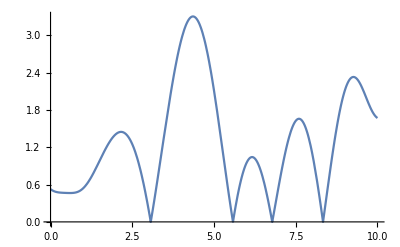
{30.0398,-Graphics-}

```mathematica
AbsoluteTiming[Plot[Abs[DirichletL[200,3,1/2+I t]],{t,0,10}]]
```

```mathematica
N[DirichletL[200,3,1/2+I 1000],200]
```

-0.2186604040860651461547679934148461596433720189941840003740040626976436146729836069082159325717556203239239146839103134810281930039481580379630316787972748194342033016626154273974687537763385626071717-0.39764779637626031336232227990330136088861445495533506147368247636109346535357888992862170588737786909797963428226851724956162382848702956953562092227389211128689472620779253483729997033806076734640305 ⅈ

The difficulty is that it is unclear which character corresponds to which L-function.

```mathematica
AbsoluteTiming[Plot[Abs[DirichletL[DC[200,129],1/2+I t]],{t,0,10}]]
```

{31.4625,-Graphics-}

Notice that, while this works, it is a bit slower than before. This is because for each evaluation, the conversion from Conrey notation to Mathematica notation is repeated. One can avoid this easily by first asking for the conversion.

```mathematica
DirichletL[DC[200,129],1/2+I T]
```

DirichletL[200,3,1/2+ⅈ T]

```mathematica
RealCharacterQ[DC[200,129]]
```

False

LSeriesZeros computes many  points, and uses bisection when it finds a sign  change. But perhaps it misses some pairs of zeros!

```mathematica
LSeriesZeros[DC[200,129],Interval[{-10,10}],0.1]
```

{-9.46508,-7.96662,-6.33073,-5.03567,-4.72084,-3.12335,-0.957381,1.0981,3.06516,4.02905,5.58062,6.78141,8.10734,8.33491}

```mathematica
Length[%]
```

14

Did we find all of them? Unfortunately, NTchi is very slow if the conductor is triple digit or larger, and is even inaccurate for if the conductor or interval is too large.

```mathematica
NTchi[DC[200,129],Interval[{-10,10}]]
```

{0,7.14508}

7